### Start choosing the example:

```mathematica
t=27;
beta = 0;
A = 0.2;
(*I1=2,U1=0*)
```

### DataToEquations and the critical congestion solver

```mathematica
Data=DataG[t]
```

<|Vertices List→{1,2,3,4,5,6,7,8,9,10},Adjacency Matrix→{{0,1,0,0,0,0,0,0,0,0},{0,0,1,0,0,0,0,0,0,0},{0,0,0,1,0,0,0,0,0,0},{0,0,0,0,1,0,0,0,0,0},{0,0,0,0,0,1,0,0,0,0},{0,0,0,0,0,0,1,0,0,0},{0,0,0,0,0,0,0,1,0,0},{0,0,0,0,0,0,0,0,1,0},{0,0,0,0,0,0,0,0,0,1},{0,0,0,0,0,0,0,0,0,0}},Entrance Vertices and Currents→{{1,2}},Exit Vertices and Terminal Costs→{{10,0}},Switching Costs→{}|>

```mathematica
MFGEquations=DataToEquations[Data];//Timing
```

DataToEquations: Finished assembling strucural equations. Reducing the structural system ...

DataToEquations: Critical case ...

DataToEquations: Critical congestion solved.

DataToEquations: Done.

{0.029377,Null}

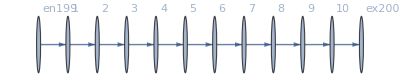

```mathematica
MFGEquations["FG"]
```

```mathematica
MFGEquations["criticalreduced1"][[2]]//KeySort
```

<|j201→2,j202→2,j203→2,j204→2,j205→2,j206→2,j207→2,j208→2,j209→2,j210→2,j211→2,j212→0,j213→0,j214→0,j215→0,j216→0,j217→0,j218→0,j219→0,j220→0,j221→0,j222→0,jt223→0,jt224→2,jt225→2,jt226→0,jt227→2,jt228→0,jt229→2,jt230→0,jt231→2,jt232→0,jt233→2,jt234→0,jt235→2,jt236→0,jt237→2,jt238→0,jt239→2,jt240→0,jt241→2,jt242→0,u243→18,u244→16,u245→14,u246→12,u247→10,u248→8,u249→6,u250→4,u251→2,u252→0,u253→18,u254→-2+18,u255→-2+16,u256→-2+14,u257→-2+12,u258→-2+10,u259→-2+8,u260→-2+6,u261→-2+4,u262→-2+2,u263→0,u264→18|>

```mathematica
Data
```

<|Vertices List→{1,2,3,4,5,6,7,8,9,10},Adjacency Matrix→{{0,1,0,0,0,0,0,0,0,0},{0,0,1,0,0,0,0,0,0,0},{0,0,0,1,0,0,0,0,0,0},{0,0,0,0,1,0,0,0,0,0},{0,0,0,0,0,1,0,0,0,0},{0,0,0,0,0,0,1,0,0,0},{0,0,0,0,0,0,0,1,0,0},{0,0,0,0,0,0,0,0,1,0},{0,0,0,0,0,0,0,0,0,1},{0,0,0,0,0,0,0,0,0,0}},Entrance Vertices and Currents→{{1,2}},Exit Vertices and Terminal Costs→{{10,0}},Switching Costs→{}|>

#### Non-linear case

```mathematica
alpha = 0;
FFR=Catch @ FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

FRX1: The Error on the nonlinear terms is 1.53837×10^-15

FRX1: The Error on the nonlinear terms is 1.53837×10^-15

<|j201→2,j202→2,j203→2,j204→2,j205→2,j206→2,j207→2,j208→2,j209→2,j210→2,j211→2,j212→0,j213→0,j214→0,j215→0,j216→0,j217→0,j218→0,j219→0,j220→0,j221→0,j222→0,jt223→0,jt224→2,jt225→2,jt226→0,jt227→2,jt228→0,jt229→2,jt230→0,jt231→2,jt232→0,jt233→2,jt234→0,jt235→2,jt236→0,jt237→2,jt238→0,jt239→2,jt240→0,jt241→2,jt242→0,u243→9.41877,u244→8.37224,u245→7.32571,u246→6.27918,u247→5.23265,u248→4.18612,u249→3.13959,u250→2.09306,u251→1.04653,u252→0,u253→9.41877,u254→8.37224,u255→7.32571,u256→6.27918,u257→5.23265,u258→4.18612,u259→3.13959,u260→2.09306,u261→1.04653,u262→0,u263→0,u264→9.41877|>

```mathematica
alpha = 0.1;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

FRX1: The Error on the nonlinear terms is 1.11022×10^-15

FRX1: The Error on the nonlinear terms is 1.11022×10^-15

<|j201→2,j202→2,j203→2,j204→2,j205→2,j206→2,j207→2,j208→2,j209→2,j210→2,j211→2,j212→0,j213→0,j214→0,j215→0,j216→0,j217→0,j218→0,j219→0,j220→0,j221→0,j222→0,jt223→0,jt224→2,jt225→2,jt226→0,jt227→2,jt228→0,jt229→2,jt230→0,jt231→2,jt232→0,jt233→2,jt234→0,jt235→2,jt236→0,jt237→2,jt238→0,jt239→2,jt240→0,jt241→2,jt242→0,u243→9.89161,u244→8.79254,u245→7.69347,u246→6.59441,u247→5.49534,u248→4.39627,u249→3.2972,u250→2.19814,u251→1.09907,u252→0,u253→9.89161,u254→8.79254,u255→7.69347,u256→6.59441,u257→5.49534,u258→4.39627,u259→3.2972,u260→2.19814,u261→1.09907,u262→0,u263→0,u264→9.89161|>

```mathematica
alpha = 0.3;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

FRX1: The Error on the nonlinear terms is 1.83103×10^-15

FRX1: The Error on the nonlinear terms is 1.83103×10^-15

<|j201→2,j202→2,j203→2,j204→2,j205→2,j206→2,j207→2,j208→2,j209→2,j210→2,j211→2,j212→0,j213→0,j214→0,j215→0,j216→0,j217→0,j218→0,j219→0,j220→0,j221→0,j222→0,jt223→0,jt224→2,jt225→2,jt226→0,jt227→2,jt228→0,jt229→2,jt230→0,jt231→2,jt232→0,jt233→2,jt234→0,jt235→2,jt236→0,jt237→2,jt238→0,jt239→2,jt240→0,jt241→2,jt242→0,u243→10.9945,u244→9.77287,u245→8.55126,u246→7.32965,u247→6.10804,u248→4.88643,u249→3.66483,u250→2.44322,u251→1.22161,u252→0,u253→10.9945,u254→9.77287,u255→8.55126,u256→7.32965,u257→6.10804,u258→4.88643,u259→3.66483,u260→2.44322,u261→1.22161,u262→0,u263→0,u264→10.9945|>

```mathematica
alpha = 0.9;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

FRX1: The Error on the nonlinear terms is 1.83103×10^-15

FRX1: The Error on the nonlinear terms is 1.83103×10^-15

<|j201→2,j202→2,j203→2,j204→2,j205→2,j206→2,j207→2,j208→2,j209→2,j210→2,j211→2,j212→0,j213→0,j214→0,j215→0,j216→0,j217→0,j218→0,j219→0,j220→0,j221→0,j222→0,jt223→0,jt224→2,jt225→2,jt226→0,jt227→2,jt228→0,jt229→2,jt230→0,jt231→2,jt232→0,jt233→2,jt234→0,jt235→2,jt236→0,jt237→2,jt238→0,jt239→2,jt240→0,jt241→2,jt242→0,u243→16.5014,u244→14.6679,u245→12.8344,u246→11.0009,u247→9.16745,u248→7.33396,u249→5.50047,u250→3.66698,u251→1.83349,u252→0,u253→16.5014,u254→14.6679,u255→12.8344,u256→11.0009,u257→9.16745,u258→7.33396,u259→5.50047,u260→3.66698,u261→1.83349,u262→0,u263→0,u264→16.5014|>

```mathematica
alpha = 1;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

FRX1: The Error on the nonlinear terms is 6.66134×10^-15

<|j201→2,j202→2,j203→2,j204→2,j205→2,j206→2,j207→2,j208→2,j209→2,j210→2,j211→2,j212→0,j213→0,j214→0,j215→0,j216→0,j217→0,j218→0,j219→0,j220→0,j221→0,j222→0,jt223→0,jt224→2,jt225→2,jt226→0,jt227→2,jt228→0,jt229→2,jt230→0,jt231→2,jt232→0,jt233→2,jt234→0,jt235→2,jt236→0,jt237→2,jt238→0,jt239→2,jt240→0,jt241→2,jt242→0,u243→18,u244→16,u245→14,u246→12,u247→10,u248→8,u249→6,u250→4,u251→2,u252→0,u253→18,u254→16,u255→14,u256→12,u257→10,u258→8,u259→6,u260→4,u261→2,u262→0,u263→0,u264→18|>

```mathematica
alpha = 1.2;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

FRX1: The Error on the nonlinear terms is 3.58036×10^-15

FRX1: The Error on the nonlinear terms is 3.58036×10^-15

<|j201→2,j202→2,j203→2,j204→2,j205→2,j206→2,j207→2,j208→2,j209→2,j210→2,j211→2,j212→0,j213→0,j214→0,j215→0,j216→0,j217→0,j218→0,j219→0,j220→0,j221→0,j222→0,jt223→0,jt224→2,jt225→2,jt226→0,jt227→2,jt228→0,jt229→2,jt230→0,jt231→2,jt232→0,jt233→2,jt234→0,jt235→2,jt236→0,jt237→2,jt238→0,jt239→2,jt240→0,jt241→2,jt242→0,u243→21.9838,u244→19.5412,u245→17.0985,u246→14.6559,u247→12.2132,u248→9.77058,u249→7.32794,u250→4.88529,u251→2.44265,u252→0,u253→21.9838,u254→19.5412,u255→17.0985,u256→14.6559,u257→12.2132,u258→9.77058,u259→7.32794,u260→4.88529,u261→2.44265,u262→0,u263→0,u264→21.9838|>

```mathematica
alpha = 1.5;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

FRX1: The Error on the nonlinear terms is 6.04027×10^-15

FRX1: The Error on the nonlinear terms is 6.04027×10^-15

<|j201→2,j202→2,j203→2,j204→2,j205→2,j206→2,j207→2,j208→2,j209→2,j210→2,j211→2,j212→0,j213→0,j214→0,j215→0,j216→0,j217→0,j218→0,j219→0,j220→0,j221→0,j222→0,jt223→0,jt224→2,jt225→2,jt226→0,jt227→2,jt228→0,jt229→2,jt230→0,jt231→2,jt232→0,jt233→2,jt234→0,jt235→2,jt236→0,jt237→2,jt238→0,jt239→2,jt240→0,jt241→2,jt242→0,u243→32.7845,u244→29.1418,u245→25.4991,u246→21.8564,u247→18.2136,u248→14.5709,u249→10.9282,u250→7.28546,u251→3.64273,u252→0,u253→32.7845,u254→29.1418,u255→25.4991,u256→21.8564,u257→18.2136,u258→14.5709,u259→10.9282,u260→7.28546,u261→3.64273,u262→0,u263→0,u264→32.7845|>

```mathematica
alpha = 1.6;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

FRX1: The Error on the nonlinear terms is 4.44089×10^-15

FRX1: The Error on the nonlinear terms is 4.44089×10^-15

<|j201→2,j202→2,j203→2,j204→2,j205→2,j206→2,j207→2,j208→2,j209→2,j210→2,j211→2,j212→0,j213→0,j214→0,j215→0,j216→0,j217→0,j218→0,j219→0,j220→0,j221→0,j222→0,jt223→0,jt224→2,jt225→2,jt226→0,jt227→2,jt228→0,jt229→2,jt230→0,jt231→2,jt232→0,jt233→2,jt234→0,jt235→2,jt236→0,jt237→2,jt238→0,jt239→2,jt240→0,jt241→2,jt242→0,u243→39.1116,u244→34.7659,u245→30.4201,u246→26.0744,u247→21.7287,u248→17.3829,u249→13.0372,u250→8.69147,u251→4.34573,u252→0,u253→39.1116,u254→34.7659,u255→30.4201,u256→26.0744,u257→21.7287,u258→17.3829,u259→13.0372,u260→8.69147,u261→4.34573,u262→0,u263→0,u264→39.1116|>

```mathematica
alpha = 1.6001;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],200,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

FRX1: The Error on the nonlinear terms is 6.15348×10^-15

FRX1: The Error on the nonlinear terms is 6.15348×10^-15

<|j201→2,j202→2,j203→2,j204→2,j205→2,j206→2,j207→2,j208→2,j209→2,j210→2,j211→2,j212→0,j213→0,j214→0,j215→0,j216→0,j217→0,j218→0,j219→0,j220→0,j221→0,j222→0,jt223→0,jt224→2,jt225→2,jt226→0,jt227→2,jt228→0,jt229→2,jt230→0,jt231→2,jt232→0,jt233→2,jt234→0,jt235→2,jt236→0,jt237→2,jt238→0,jt239→2,jt240→0,jt241→2,jt242→0,u243→39.1191,u244→34.7725,u245→30.426,u246→26.0794,u247→21.7328,u248→17.3863,u249→13.0397,u250→8.69314,u251→4.34657,u252→0,u253→39.1191,u254→34.7725,u255→30.426,u256→26.0794,u257→21.7328,u258→17.3863,u259→13.0397,u260→8.69314,u261→4.34657,u262→0,u263→0,u264→39.1191|>

```mathematica
alpha = 2;
FixedPoint[FixedReduceX1[MFGEquations],FFR,10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

FRX1: The Error on the nonlinear terms is 2.86429×10^-14

FRX1: The Error on the nonlinear terms is 2.86429×10^-14

<|j201→2,j202→2,j203→2,j204→2,j205→2,j206→2,j207→2,j208→2,j209→2,j210→2,j211→2,j212→0,j213→0,j214→0,j215→0,j216→0,j217→0,j218→0,j219→0,j220→0,j221→0,j222→0,jt223→0,jt224→2,jt225→2,jt226→0,jt227→2,jt228→0,jt229→2,jt230→0,jt231→2,jt232→0,jt233→2,jt234→0,jt235→2,jt236→0,jt237→2,jt238→0,jt239→2,jt240→0,jt241→2,jt242→0,u243→147.359,u244→130.986,u245→114.612,u246→98.2392,u247→81.866,u248→65.4928,u249→49.1196,u250→32.7464,u251→16.3732,u252→0,u253→147.359,u254→130.986,u255→114.612,u256→98.2392,u257→81.866,u258→65.4928,u259→49.1196,u260→32.7464,u261→16.3732,u262→0,u263→0,u264→147.359|>

```mathematica
alpha = 1.605;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

FRX1: The Error on the nonlinear terms is 4.44089×10^-15

FRX1: The Error on the nonlinear terms is 4.44089×10^-15

<|j201→2,j202→2,j203→2,j204→2,j205→2,j206→2,j207→2,j208→2,j209→2,j210→2,j211→2,j212→0,j213→0,j214→0,j215→0,j216→0,j217→0,j218→0,j219→0,j220→0,j221→0,j222→0,jt223→0,jt224→2,jt225→2,jt226→0,jt227→2,jt228→0,jt229→2,jt230→0,jt231→2,jt232→0,jt233→2,jt234→0,jt235→2,jt236→0,jt237→2,jt238→0,jt239→2,jt240→0,jt241→2,jt242→0,u243→39.4907,u244→35.1029,u245→30.715,u246→26.3271,u247→21.9393,u248→17.5514,u249→13.1636,u250→8.77571,u251→4.38786,u252→0,u253→39.4907,u254→35.1029,u255→30.715,u256→26.3271,u257→21.9393,u258→17.5514,u259→13.1636,u260→8.77571,u261→4.38786,u262→0,u263→0,u264→39.4907|>

```mathematica
alpha = 1.61;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

FRX1: The Error on the nonlinear terms is 7.16072×10^-15

FRX1: The Error on the nonlinear terms is 7.16072×10^-15

<|j201→2,j202→2,j203→2,j204→2,j205→2,j206→2,j207→2,j208→2,j209→2,j210→2,j211→2,j212→0,j213→0,j214→0,j215→0,j216→0,j217→0,j218→0,j219→0,j220→0,j221→0,j222→0,jt223→0,jt224→2,jt225→2,jt226→0,jt227→2,jt228→0,jt229→2,jt230→0,jt231→2,jt232→0,jt233→2,jt234→0,jt235→2,jt236→0,jt237→2,jt238→0,jt239→2,jt240→0,jt241→2,jt242→0,u243→39.877,u244→35.4462,u245→31.0155,u246→26.5847,u247→22.1539,u248→17.7231,u249→13.2923,u250→8.86156,u251→4.43078,u252→0,u253→39.877,u254→35.4462,u255→31.0155,u256→26.5847,u257→22.1539,u258→17.7231,u259→13.2923,u260→8.86156,u261→4.43078,u262→0,u263→0,u264→39.877|>

```mathematica
alpha = 1.62;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

FRX1: The Error on the nonlinear terms is 0.

FRX1: The Error on the nonlinear terms is 0.

<|j201→2,j202→2,j203→2,j204→2,j205→2,j206→2,j207→2,j208→2,j209→2,j210→2,j211→2,j212→0,j213→0,j214→0,j215→0,j216→0,j217→0,j218→0,j219→0,j220→0,j221→0,j222→0,jt223→0,jt224→2,jt225→2,jt226→0,jt227→2,jt228→0,jt229→2,jt230→0,jt231→2,jt232→0,jt233→2,jt234→0,jt235→2,jt236→0,jt237→2,jt238→0,jt239→2,jt240→0,jt241→2,jt242→0,u243→40.672,u244→36.1529,u245→31.6338,u246→27.1147,u247→22.5956,u248→18.0765,u249→13.5573,u250→9.03823,u251→4.51911,u252→0,u253→40.672,u254→36.1529,u255→31.6338,u256→27.1147,u257→22.5956,u258→18.0765,u259→13.5573,u260→9.03823,u261→4.51911,u262→0,u263→0,u264→40.672|>

```mathematica
alpha = 1.65;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

FRX1: The Error on the nonlinear terms is 4.44089×10^-15

FRX1: The Error on the nonlinear terms is 4.44089×10^-15

<|j201→2,j202→2,j203→2,j204→2,j205→2,j206→2,j207→2,j208→2,j209→2,j210→2,j211→2,j212→0,j213→0,j214→0,j215→0,j216→0,j217→0,j218→0,j219→0,j220→0,j221→0,j222→0,jt223→0,jt224→2,jt225→2,jt226→0,jt227→2,jt228→0,jt229→2,jt230→0,jt231→2,jt232→0,jt233→2,jt234→0,jt235→2,jt236→0,jt237→2,jt238→0,jt239→2,jt240→0,jt241→2,jt242→0,u243→43.2526,u244→38.4467,u245→33.6409,u246→28.8351,u247→24.0292,u248→19.2234,u249→14.4175,u250→9.61169,u251→4.80584,u252→0,u253→43.2526,u254→38.4467,u255→33.6409,u256→28.8351,u257→24.0292,u258→19.2234,u259→14.4175,u260→9.61169,u261→4.80584,u262→0,u263→0,u264→43.2526|>

```mathematica
alpha = 1.7;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

FRX1: The Error on the nonlinear terms is 9.3996×10^-15

FRX1: The Error on the nonlinear terms is 9.3996×10^-15

<|j201→2,j202→2,j203→2,j204→2,j205→2,j206→2,j207→2,j208→2,j209→2,j210→2,j211→2,j212→0,j213→0,j214→0,j215→0,j216→0,j217→0,j218→0,j219→0,j220→0,j221→0,j222→0,jt223→0,jt224→2,jt225→2,jt226→0,jt227→2,jt228→0,jt229→2,jt230→0,jt231→2,jt232→0,jt233→2,jt234→0,jt235→2,jt236→0,jt237→2,jt238→0,jt239→2,jt240→0,jt241→2,jt242→0,u243→48.3351,u244→42.9645,u245→37.594,u246→32.2234,u247→26.8528,u248→21.4823,u249→16.1117,u250→10.7411,u251→5.37057,u252→0,u253→48.3351,u254→42.9645,u255→37.594,u256→32.2234,u257→26.8528,u258→21.4823,u259→16.1117,u260→10.7411,u261→5.37057,u262→0,u263→0,u264→48.3351|>

```mathematica
alpha = 1.8;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

FRX1: The Error on the nonlinear terms is 1.06581×10^-14

FRX1: The Error on the nonlinear terms is 1.06581×10^-14

<|j201→2,j202→2,j203→2,j204→2,j205→2,j206→2,j207→2,j208→2,j209→2,j210→2,j211→2,j212→0,j213→0,j214→0,j215→0,j216→0,j217→0,j218→0,j219→0,j220→0,j221→0,j222→0,jt223→0,jt224→2,jt225→2,jt226→0,jt227→2,jt228→0,jt229→2,jt230→0,jt231→2,jt232→0,jt233→2,jt234→0,jt235→2,jt236→0,jt237→2,jt238→0,jt239→2,jt240→0,jt241→2,jt242→0,u243→62.9182,u244→55.9273,u245→48.9364,u246→41.9455,u247→34.9546,u248→27.9637,u249→20.9727,u250→13.9818,u251→6.99091,u252→0,u253→62.9182,u254→55.9273,u255→48.9364,u256→41.9455,u257→34.9546,u258→27.9637,u259→20.9727,u260→13.9818,u261→6.99091,u262→0,u263→0,u264→62.9182|>

```mathematica
alpha = 1.9;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

FRX1: The Error on the nonlinear terms is 1.58882×10^-14

FRX1: The Error on the nonlinear terms is 1.58882×10^-14

<|j201→2,j202→2,j203→2,j204→2,j205→2,j206→2,j207→2,j208→2,j209→2,j210→2,j211→2,j212→0,j213→0,j214→0,j215→0,j216→0,j217→0,j218→0,j219→0,j220→0,j221→0,j222→0,jt223→0,jt224→2,jt225→2,jt226→0,jt227→2,jt228→0,jt229→2,jt230→0,jt231→2,jt232→0,jt233→2,jt234→0,jt235→2,jt236→0,jt237→2,jt238→0,jt239→2,jt240→0,jt241→2,jt242→0,u243→89.0472,u244→79.153,u245→69.2589,u246→59.3648,u247→49.4707,u248→39.5765,u249→29.6824,u250→19.7883,u251→9.89413,u252→0,u253→89.0472,u254→79.153,u255→69.2589,u256→59.3648,u257→49.4707,u258→39.5765,u259→29.6824,u260→19.7883,u261→9.89413,u262→0,u263→0,u264→89.0472|>

```mathematica
alpha = 2;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],20,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

FRX1: The Error on the nonlinear terms is 2.86429×10^-14

FRX1: The Error on the nonlinear terms is 2.86429×10^-14

<|j201→2,j202→2,j203→2,j204→2,j205→2,j206→2,j207→2,j208→2,j209→2,j210→2,j211→2,j212→0,j213→0,j214→0,j215→0,j216→0,j217→0,j218→0,j219→0,j220→0,j221→0,j222→0,jt223→0,jt224→2,jt225→2,jt226→0,jt227→2,jt228→0,jt229→2,jt230→0,jt231→2,jt232→0,jt233→2,jt234→0,jt235→2,jt236→0,jt237→2,jt238→0,jt239→2,jt240→0,jt241→2,jt242→0,u243→147.359,u244→130.986,u245→114.612,u246→98.2392,u247→81.866,u248→65.4928,u249→49.1196,u250→32.7464,u251→16.3732,u252→0,u253→147.359,u254→130.986,u255→114.612,u256→98.2392,u257→81.866,u258→65.4928,u259→49.1196,u260→32.7464,u261→16.3732,u262→0,u263→0,u264→147.359|>

### What we this plot for?

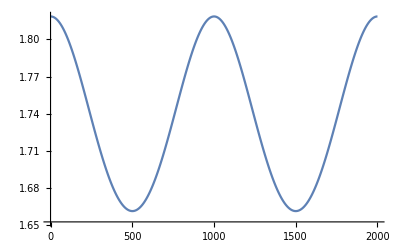

```mathematica
ListLinePlot [Values @ First @ FindRoot [Parameters["H[x,p,m]"][#,-2/(m^(1-.5)),m],{m,1}]& /@Table[i,{i,0,1,1/2000}]]
```

j from critical cong. use this in the rhs. maybe some jt is now defined and changes the value of that initial j. so, if we use the association to update the solution rules, we will alwas retrieve the most up - to - date values.